```mathematica
m=UnitConvert[Quantity["ElectronMass"]]
```

9.109383×10^-31

```mathematica
e0=UnitConvert[m*Quantity["SpeedOfLight"]^2]
```

8.187105×10^-14

```mathematica
pmax=UnitConvert[Quantity[1*^6,"ElectronVolt"]/Quantity["SpeedOfLight"]]
```

1.068857×10^-21

```mathematica
eclassical[p_]:=UnitConvert[p^2/(2m)]
```

```mathematica
ephoton[p_]:=UnitConvert[Quantity["SpeedOfLight"]p]
```

```mathematica
eelectron[p_]:=UnitConvert[Sqrt[e0^2+Quantity["SpeedOfLight"]^2p^2]-e0]
```

```mathematica
eclassical[pmax]//UnitConvert
```

6.27076×10^-13

```mathematica
ephoton[pmax]//UnitConvert
```

3.204353×10^-13

2.488579×10^-13

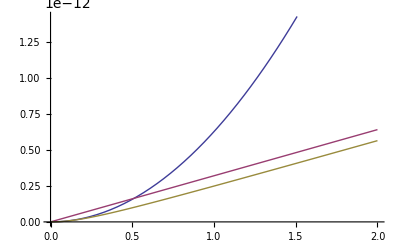

```mathematica
eelectron[pmax]//UnitConvert//QuantityMagnitude
```

WolframAlphaQueryResults

Compton wavelength | 2.21 pm  (picometers)
= 8.702×10^-11 inches
= 2.21×10^-12 meters

```mathematica
k=2Pi/Quantity[2.21*^-12,"Meter"]
```

2.84307×10^12

```mathematica
hkc=UnitConvert[Quantity["PlanckConstant"]k/(2Pi)]
```

2.99822×10^-22

```mathematica
hkcc=UnitConvert[hkc*Quantity["SpeedOfLight"]]
```

8.98844×10^-14

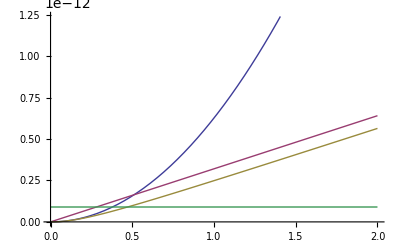

```mathematica
Plot[
{
QuantityMagnitude[eclassical[x pmax]],
QuantityMagnitude[ephoton[x pmax]],
QuantityMagnitude[eelectron[x pmax]],
QuantityMagnitude[hkcc]
},{x,0,2}]
```